# Binary Tree Schur Transform

## Clebsch-Gordan coefficients for GCG (General Clebsch-Gordan Transform)

Here we implement the General Clebsch-Gordan (GCG) transform for spin subspaces with total spins j1 and j2.

Some supportive functions:

Given the total number of boxes (qubits) ' n' in Semi-Standard Young Tableau (SSYT) and the number of boxes in the second row ' l2', computes the number of SSYT' s with these parameters .

```mathematica
NumSSYT[n_,l2_]:=n-2*l2+1;
```

Given the total number of boxes (qubits) 'n' in Standard Young Tableau (SYT) and the number of boxes in the second row 'l2', computes the number of SYT's with these parameters.

```mathematica
NumSYT[n_,l2_]:= Binomial[n+1,l2]*(n-2*l2+1)/(n+1);
```

Direct sum of a given list of matrices.

```mathematica
DirectSum[lst_]:=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@lst];
```

GCG transform, acts on spin subspaces j1 and j2, which represent some binary trees with total spins j1 and j2 on the final leaf and dimensions d1 and d2. GCG transform acts like merging the two trees together with all possible values of J for the final leaf of the merged tree, specifically J in [Abs(j1-j2) ; j1+j2]. The dimension of the merged tree is d1 + d2.

```mathematica
Off[ClebschGordan::phy]
GCGTransform[j1_,j2_]:=SparseArray[Join@@Table[Transpose@Flatten[Table[ClebschGordan[{j1,m1},{j2,m2},{J,m}],{m1,j1,-j1,-1},{m2,j2,-j2,-1},{m,J,-J,-1}],{{1,2},{3}}],{J,j1+j2,Abs[j1-j2],-1}]]
```

Direct sum of multiple GCG transforms for n qubits, in order to capture all possible results for merging all possible pairs of binary trees for n/2 qubits, which themselves are results of all possible pairs and so on. Essentially this is just the direct of all possible GCG transforms on all pairs of leaves. Direct sum is applied to GCG’s in this order (example for BigGCGTransform[8]):
DirectSum@{cg22, cg12, cg12, cg12, cg02, cg02, cg21, cg11, cg11, cg11, cg01, cg01, cg21, cg11, cg11, cg11, cg01, cg01, cg21, cg11, cg11, cg11, cg01, cg01, cg20, cg10, cg10, cg10, cg00, cg00, cg20, cg10, cg10, cg10, cg00, cg00} ,
where cgij = GCGTransform[i, j].
It is later explained why the order was chosen in this way.

```mathematica
BigGCGTransform[n_]:=DirectSum@Flatten[Table[ConstantArray[Table[ConstantArray[GCGTransform[j1,j2],NumSYT[n/2,n/4-j1]],{j1,n/4,0,-1}],NumSYT[n/2,n/4-j2]],{j2,n/4, 0,-1}],3];
```

## Permutations for GCG

Permutation of registers A⊗B into B⊗A.

```mathematica
TensorPermutation[da_,db_]:=SparseArray[PermutationMatrix[Join@@Table[j*db+i,{i,1,db},{j,0,da-1}]]]
```

Preparatory permutation for the computational basis of n qubits, which is required because tensor product of direct sums is not the same as direct sum of tensor products: (A⊕B)⊗(C⊕D) ≠ A⊗C ⊕ B⊕D. Although, from the definition of tensor product, it is true that:  (A⊕B)⊗(C⊕D) = A⊗(C⊕D)⊕ B⊗(C⊕D). Therefore, if we change the registers after this expansion, we receive something like: (C⊕D)⊗A ⊕ (C⊕D)⊗B. In reality though, we also expand both A and B as direct sums entirely, and only then change the registers for every direct-sum-term. Therefore, we effectively turn the computational basis into a direct sum of blocks, on which we then apply the corresponding direct sum of GCG’s. The structure of the order would be as per above, mentioned in the example for BigGCGTransform (because the registers were changed, it’s essentially reverse-dictionary order but prioritising the ordering by the second register instead of the first one, because of the permutation of registers).

```mathematica
GCGPermutation[n_]:=Module[{M},
If[n==2, M=SparseArray[IdentityMatrix[4]];,
M=DirectSum@Flatten[Table[ConstantArray[TensorPermutation[NumSSYT[n/2,λ2],2^(n/2)],NumSYT[n/2,λ2]],{λ2,0,Quotient[n/2,2]}],1];
];
M
]
```

The above permutations are not sufficient for the Binary Tree Schur, as we still have to permute the final blocks (formed after the application of the direct sum of GCG’s onto bigger blocks) according to the binary tree order (also by their dimensions from highest to lowest).
In this step we implement a representation of the Binary Tree Schur basis that uniquely defines every independent basis state. This representation is equivalent to representing each basis element with a spin-coupling binary tree with a spin projection associated to every tree-basis element.
We also define the auxiliary functions that help to manipulate and construct new basis elements for higher number of qubits from lower number of qubits by merging trees.
Using this representation we then order the result after the application of the merging function, and then use the same ordering to sort the final blocks.

Every element of the basis list “BTBasisn” for some number of qubits n is some basis element, i.e. a binary tree with a spin-projection (magnetic) number. Specifically, any basis element is a list of levels of the binary tree ordered from highest to lowest level, with each level listing all the entries on this level, and also at the end of the basis element we have a magnetic number associated with this binary tree (which can be in range [-J; J] for the final leaf having the total spin J). In order to minimise the number of entries defining the basis element, we also omit listing the first level of the binary tree, because the first level is always just {1/2, 1/2, 1/2, ... , 1/2}.
For example, for 4 qubits the basis BTBasis4 would look like:
{{2,{1,1},2}, {2,{1,1},1}, {2,{1,1},0}, {2,{1,1},-1}, {2,{1,1},-2}, {1,{1,1},1}, {1,{1,1},0}, {1,{1,1},-1}, {1,{1,0},1}, {1,{1,0},0}, {1,{1,0},-1}, {1,{0,1},1}, {1,{0,1},0}, {1,{0,1},-1}, {0,{1,1},0}, {0,{0,0},0}}
The order of this basis is just reverse dictionary order.
Dissecting each level, on the example of {1,{1,0},-1}:

first entry represents the total spin J of the last-level leaf and generally the total spin of this binary tree;

second entry represents all the spins on the previous level, in this case 1 and 0;

third entry represents the magnetic number, i.e. the total spin projection M of this tree, which can be from -J to J, in this case it is M = -1.

```mathematica
BTBasis2={{1,1},{1,0},{1,-1},{0,0}}
```

{{1,1},{1,0},{1,-1},{0,0}}

“Merging” function for two trees bt1 and bt2 with some total spins J1 and J2, results in the direct sum of all possible combinations with all possible magnetic numbers.

```mathematica
BasisGCG[bt1_,bt2_]:=Module[{},
Flatten[Table[{J,{bt1[[1]],bt2[[1]]},Sequence@@Table[Join[bt1[[i]],bt2[[i]]],{i,2,Length[bt1]-1}] ,m},{J,bt1[[1]]+bt2[[1]],Abs[bt1[[1]]-bt2[[1]]],-1},{m,J,-J,-1}],1]
]
```

Basis extension from the initial (sorted) basis for n/2 qubits resulting in the final (unsorted) basis for n qubits. Essentially this imitates the order seen in the matrix blocks that we have to permute, so we can extract this order later.

```mathematica
BTSchurExtendBasis[btb_,n_]:=Module[{counter1,counter2},
If[n==2, BTBasis2,
counter2=0;
Flatten[
Table[
counter2=counter2+NumSSYT[n/2,λ22];
counter1=0;
Table[
counter1=counter1+NumSSYT[n/2,λ21];
BasisGCG[btb[[counter1]],btb[[counter2]]],
{λ21,0,Quotient[n/2,2]},
{NumSYT[n/2,λ21]}
],
{λ22,0,Quotient[n/2,2]},
{NumSYT[n/2,λ22]}
],
4]
]
]
```

## Binary Tree Schur Transform through GCG, tensor permutation (GCGPermutation) and BTSchurExtend Basis

In this step we implement the Binary Tree Schur Transform for n qubits, by combining all the previous steps, with first multiplying (recursively) the BigGCG with the permutation for the tensor product and the Tensor product of two Binary Tree Schurs for the previous step (dimension n/2 for both), and then multiplying from the left by the permutation matrix of the ordering recovered from the Binary Tree basis.

```mathematica
BBTSchur[n_]:=Module[{BBTSchurTrans,btb,m=2},
BBTSchurTrans=SparseArray[IdentityMatrix[2]];
btb=BTBasis2;
Do[BBTSchurTrans=PermutationMatrix[Reverse@Ordering[btb=BTSchurExtendBasis[Reverse@Sort@btb,m]]] . BigGCGTransform[m].GCGPermutation[m]. KroneckerProduct[BBTSchurTrans,BBTSchurTrans];
m=m*2;,
Log[2,n]];
BBTSchurTrans
]
```

## Workspace

```mathematica
(* Check the timing and unitarity *)
```

```mathematica
Timing[BBTSchur[8];]
```

{0.078125,Null}

```mathematica
BBTSchur[8].BBTSchur[8]ᵀ ==IdentityMatrix[256]
```

True

```mathematica
(* TensU2[n] is U2Mat tensored with itself n times *)
U2Mat = {{a,b},{c,d}};
TensU2[n_]:= Module[{M=U2Mat},For[i=1,i< n, i++,M= KroneckerProduct[M,U2Mat]]; Return[M]]
```

```mathematica
(* GenSwap[k,n] is a permutation matrix that permutes k and k+1 qubits in a system of n qubits *)
Swap = {{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};
GenSwap[k_,n_]:=Module[{PerMat},
     For[i=1;PerMat=Swap,i<k,i++,PerMat=KroneckerProduct[IdentityMatrix[2],PerMat]];
For[i=k,i<n-1,i++,PerMat=KroneckerProduct[PerMat,IdentityMatrix[2]]];
Return[PerMat];
]
```

```mathematica
(* Check block diagonalisation for unitary group *)
```

```mathematica
TTensU2=Simplify[BBTSchur[8].TensU2[8].BBTSchur[8]ᵀ];
```

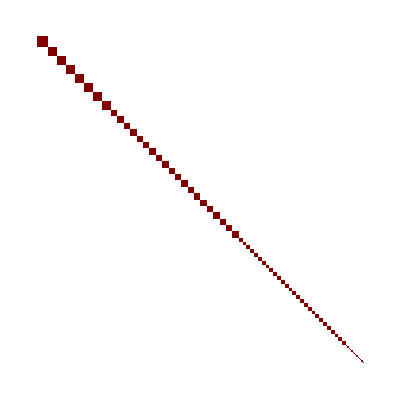

```mathematica
TTensU2 // ArrayPlot
```

```mathematica
(* Analyse the blocks and check that the multiplicity and dimension order is correct *)
```

```mathematica
TensBlockMatrix=BlockDiagonalMatrix[TTensU2];
Table[Length[TensBlockMatrix["Blocks"][[i]]],{i,1,Length[TensBlockMatrix["Blocks"]]}]
Union@TensBlockMatrix["Blocks"];
MatrixForm/@%
```

{9,7,7,7,7,7,7,7,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{((b c-a d)^4),(a^2 (-b c+a d)^3 | √2 a b (-b c+a d)^3 | -b^2 (b c-a d)^3
√2 a c (-b c+a d)^3 | -(b c-a d)^3 (b c+a d) | -√2 b d (b c-a d)^3
-c^2 (b c-a d)^3 | -√2 c d (b c-a d)^3 | d^2 (-b c+a d)^3),(a^4 (b c-a d)^2 | 2 a^3 b (b c-a d)^2 | √6 a^2 b^2 (b c-a d)^2 | 2 a b^3 (b c-a d)^2 | b^4 (b c-a d)^2
2 a^3 c (b c-a d)^2 | a^2 (b c-a d)^2 (3 b c+a d) | √6 a b (b c-a d)^2 (b c+a d) | b^2 (b c-a d)^2 (b c+3 a d) | 2 b^3 d (b c-a d)^2
√6 a^2 c^2 (b c-a d)^2 | √6 a c (b c-a d)^2 (b c+a d) | (b c-a d)^2 (b^2 c^2+4 a b c d+a^2 d^2) | √6 b d (b c-a d)^2 (b c+a d) | √6 b^2 d^2 (b c-a d)^2
2 a c^3 (b c-a d)^2 | c^2 (b c-a d)^2 (b c+3 a d) | √6 c d (b c-a d)^2 (b c+a d) | d^2 (b c-a d)^2 (3 b c+a d) | 2 b d^3 (b c-a d)^2
c^4 (b c-a d)^2 | 2 c^3 d (b c-a d)^2 | √6 c^2 d^2 (b c-a d)^2 | 2 c d^3 (b c-a d)^2 | d^4 (b c-a d)^2),(a^6 (-b c+a d) | √6 a^5 b (-b c+a d) | √15 a^4 b^2 (-b c+a d) | 2 √5 a^3 b^3 (-b c+a d) | √15 a^2 b^4 (-b c+a d) | √6 a b^5 (-b c+a d) | b^6 (-b c+a d)
√6 a^5 c (-b c+a d) | a^4 (-5 b^2 c^2+4 a b c d+a^2 d^2) | √10 a^3 b (-2 b^2 c^2+a b c d+a^2 d^2) | √30 a^2 b^2 (-b^2 c^2+a^2 d^2) | √10 a b^3 (-b^2 c^2-a b c d+2 a^2 d^2) | -b^4 (b^2 c^2+4 a b c d-5 a^2 d^2) | √6 b^5 d (-b c+a d)
√15 a^4 c^2 (-b c+a d) | √10 a^3 c (-2 b^2 c^2+a b c d+a^2 d^2) | a^2 (-6 b^3 c^3-2 a b^2 c^2 d+7 a^2 b c d^2+a^3 d^3) | 2 √3 a b (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | b^2 (-b^3 c^3-7 a b^2 c^2 d+2 a^2 b c d^2+6 a^3 d^3) | -√10 b^3 d (b^2 c^2+a b c d-2 a^2 d^2) | √15 b^4 d^2 (-b c+a d)
2 √5 a^3 c^3 (-b c+a d) | √30 a^2 c^2 (-b^2 c^2+a^2 d^2) | 2 √3 a c (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | -b^4 c^4-8 a b^3 c^3 d+8 a^3 b c d^3+a^4 d^4 | -2 √3 b d (b^3 c^3+2 a b^2 c^2 d-2 a^2 b c d^2-a^3 d^3) | √30 b^2 d^2 (-b^2 c^2+a^2 d^2) | 2 √5 b^3 d^3 (-b c+a d)
√15 a^2 c^4 (-b c+a d) | √10 a c^3 (-b^2 c^2-a b c d+2 a^2 d^2) | c^2 (-b^3 c^3-7 a b^2 c^2 d+2 a^2 b c d^2+6 a^3 d^3) | 2 √3 c d (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | d^2 (-6 b^3 c^3-2 a b^2 c^2 d+7 a^2 b c d^2+a^3 d^3) | √10 b d^3 (-2 b^2 c^2+a b c d+a^2 d^2) | √15 b^2 d^4 (-b c+a d)
√6 a c^5 (-b c+a d) | -c^4 (b^2 c^2+4 a b c d-5 a^2 d^2) | -√10 c^3 d (b^2 c^2+a b c d-2 a^2 d^2) | √30 c^2 d^2 (-b^2 c^2+a^2 d^2) | -√10 c d^3 (2 b^2 c^2-a b c d-a^2 d^2) | d^4 (-5 b^2 c^2+4 a b c d+a^2 d^2) | √6 b d^5 (-b c+a d)
c^6 (-b c+a d) | √6 c^5 d (-b c+a d) | -√15 c^4 d^2 (b c-a d) | -2 √5 c^3 d^3 (b c-a d) | -√15 c^2 d^4 (b c-a d) | √6 c d^5 (-b c+a d) | d^6 (-b c+a d)),(a^6 (-b c+a d) | √6 a^5 b (-b c+a d) | √15 a^4 b^2 (-b c+a d) | 2 √5 a^3 b^3 (-b c+a d) | √15 a^2 b^4 (-b c+a d) | √6 a b^5 (-b c+a d) | b^6 (-b c+a d)
√6 a^5 c (-b c+a d) | a^4 (-5 b^2 c^2+4 a b c d+a^2 d^2) | √10 a^3 b (-2 b^2 c^2+a b c d+a^2 d^2) | √30 a^2 b^2 (-b^2 c^2+a^2 d^2) | √10 a b^3 (-b^2 c^2-a b c d+2 a^2 d^2) | -b^4 (b^2 c^2+4 a b c d-5 a^2 d^2) | √6 b^5 d (-b c+a d)
√15 a^4 c^2 (-b c+a d) | √10 a^3 c (-2 b^2 c^2+a b c d+a^2 d^2) | a^2 (-6 b^3 c^3-2 a b^2 c^2 d+7 a^2 b c d^2+a^3 d^3) | 2 √3 a b (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | b^2 (-b^3 c^3-7 a b^2 c^2 d+2 a^2 b c d^2+6 a^3 d^3) | -√10 b^3 d (b^2 c^2+a b c d-2 a^2 d^2) | √15 b^4 d^2 (-b c+a d)
2 √5 a^3 c^3 (-b c+a d) | √30 a^2 c^2 (-b^2 c^2+a^2 d^2) | 2 √3 a c (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | -b^4 c^4-8 a b^3 c^3 d+8 a^3 b c d^3+a^4 d^4 | -2 √3 b d (b^3 c^3+2 a b^2 c^2 d-2 a^2 b c d^2-a^3 d^3) | √30 b^2 d^2 (-b^2 c^2+a^2 d^2) | 2 √5 b^3 d^3 (-b c+a d)
√15 a^2 c^4 (-b c+a d) | √10 a c^3 (-b^2 c^2-a b c d+2 a^2 d^2) | c^2 (-b^3 c^3-7 a b^2 c^2 d+2 a^2 b c d^2+6 a^3 d^3) | 2 √3 c d (-b^3 c^3-2 a b^2 c^2 d+2 a^2 b c d^2+a^3 d^3) | d^2 (-6 b^3 c^3-2 a b^2 c^2 d+7 a^2 b c d^2+a^3 d^3) | √10 b d^3 (-2 b^2 c^2+a b c d+a^2 d^2) | √15 b^2 d^4 (-b c+a d)
√6 a c^5 (-b c+a d) | -c^4 (b^2 c^2+4 a b c d-5 a^2 d^2) | -√10 c^3 d (b^2 c^2+a b c d-2 a^2 d^2) | √30 c^2 d^2 (-b^2 c^2+a^2 d^2) | √10 c d^3 (-2 b^2 c^2+a b c d+a^2 d^2) | d^4 (-5 b^2 c^2+4 a b c d+a^2 d^2) | √6 b d^5 (-b c+a d)
c^6 (-b c+a d) | -√6 c^5 d (b c-a d) | -√15 c^4 d^2 (b c-a d) | -2 √5 c^3 d^3 (b c-a d) | -√15 c^2 d^4 (b c-a d) | -√6 c d^5 (b c-a d) | d^6 (-b c+a d)),(a^8 | 2 √2 a^7 b | 2 √7 a^6 b^2 | 2 √14 a^5 b^3 | √70 a^4 b^4 | 2 √14 a^3 b^5 | 2 √7 a^2 b^6 | 2 √2 a b^7 | b^8
2 √2 a^7 c | a^6 (7 b c+a d) | √14 a^5 b (3 b c+a d) | √7 a^4 b^2 (5 b c+3 a d) | 2 √35 a^3 b^3 (b c+a d) | √7 a^2 b^4 (3 b c+5 a d) | √14 a b^5 (b c+3 a d) | b^6 (b c+7 a d) | 2 √2 b^7 d
2 √7 a^6 c^2 | √14 a^5 c (3 b c+a d) | a^4 (15 b^2 c^2+12 a b c d+a^2 d^2) | √2 a^3 b (10 b^2 c^2+15 a b c d+3 a^2 d^2) | √10 a^2 b^2 (3 b^2 c^2+8 a b c d+3 a^2 d^2) | √2 a b^3 (3 b^2 c^2+15 a b c d+10 a^2 d^2) | b^4 (b^2 c^2+12 a b c d+15 a^2 d^2) | √14 b^5 d (b c+3 a d) | 2 √7 b^6 d^2
2 √14 a^5 c^3 | √7 a^4 c^2 (5 b c+3 a d) | √2 a^3 c (10 b^2 c^2+15 a b c d+3 a^2 d^2) | a^2 (10 b^3 c^3+30 a b^2 c^2 d+15 a^2 b c d^2+a^3 d^3) | 2 √5 a b (b^3 c^3+6 a b^2 c^2 d+6 a^2 b c d^2+a^3 d^3) | b^2 (b^3 c^3+15 a b^2 c^2 d+30 a^2 b c d^2+10 a^3 d^3) | √2 b^3 d (3 b^2 c^2+15 a b c d+10 a^2 d^2) | √7 b^4 d^2 (3 b c+5 a d) | 2 √14 b^5 d^3
√70 a^4 c^4 | 2 √35 a^3 c^3 (b c+a d) | √10 a^2 c^2 (3 b^2 c^2+8 a b c d+3 a^2 d^2) | 2 √5 a c (b^3 c^3+6 a b^2 c^2 d+6 a^2 b c d^2+a^3 d^3) | b^4 c^4+16 a b^3 c^3 d+36 a^2 b^2 c^2 d^2+16 a^3 b c d^3+a^4 d^4 | 2 √5 b d (b^3 c^3+6 a b^2 c^2 d+6 a^2 b c d^2+a^3 d^3) | √10 b^2 d^2 (3 b^2 c^2+8 a b c d+3 a^2 d^2) | 2 √35 b^3 d^3 (b c+a d) | √70 b^4 d^4
2 √14 a^3 c^5 | √7 a^2 c^4 (3 b c+5 a d) | √2 a c^3 (3 b^2 c^2+15 a b c d+10 a^2 d^2) | c^2 (b^3 c^3+15 a b^2 c^2 d+30 a^2 b c d^2+10 a^3 d^3) | 2 √5 c d (b^3 c^3+6 a b^2 c^2 d+6 a^2 b c d^2+a^3 d^3) | d^2 (10 b^3 c^3+30 a b^2 c^2 d+15 a^2 b c d^2+a^3 d^3) | √2 b d^3 (10 b^2 c^2+15 a b c d+3 a^2 d^2) | √7 b^2 d^4 (5 b c+3 a d) | 2 √14 b^3 d^5
2 √7 a^2 c^6 | √14 a c^5 (b c+3 a d) | c^4 (b^2 c^2+12 a b c d+15 a^2 d^2) | √2 c^3 d (3 b^2 c^2+15 a b c d+10 a^2 d^2) | √10 c^2 d^2 (3 b^2 c^2+8 a b c d+3 a^2 d^2) | √2 c d^3 (10 b^2 c^2+15 a b c d+3 a^2 d^2) | d^4 (15 b^2 c^2+12 a b c d+a^2 d^2) | √14 b d^5 (3 b c+a d) | 2 √7 b^2 d^6
2 √2 a c^7 | c^6 (b c+7 a d) | √14 c^5 d (b c+3 a d) | √7 c^4 d^2 (3 b c+5 a d) | 2 √35 c^3 d^3 (b c+a d) | √7 c^2 d^4 (5 b c+3 a d) | √14 c d^5 (3 b c+a d) | d^6 (7 b c+a d) | 2 √2 b d^7
c^8 | 2 √2 c^7 d | 2 √7 c^6 d^2 | 2 √14 c^5 d^3 | √70 c^4 d^4 | 2 √14 c^3 d^5 | 2 √7 c^2 d^6 | 2 √2 c d^7 | d^8)}

```mathematica
(* Check block diagonalisation for symmetric group *)
```

```mathematica
TGenSwap48=Simplify[BBTSchur[8].GenSwap[4,8].BBTSchur[8]ᵀ];
```

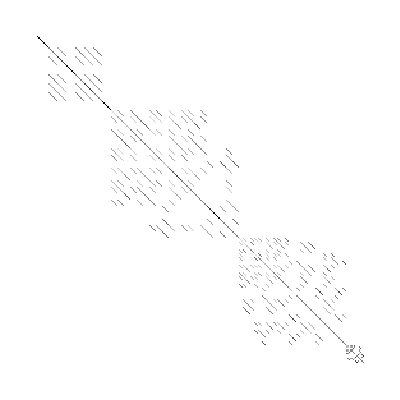

```mathematica
TGenSwap48 // ArrayPlot
```

```mathematica
(* Analyse the blocks *)
```

```mathematica
SwapBlockMatrix48=BlockDiagonalMatrix[TGenSwap48];
Union@SwapBlockMatrix48["Blocks"];
MatrixForm/@%
```

{(1),(-1/2 | (√3)/2
(√3)/2 | 1/2),(0 | -1/(√2) | -1/(√2)
-1/(√2) | 1/2 | -1/2
-1/(√2) | -1/2 | 1/2),(1/4 | -(√(3/2))/2 | (√3)/4 | -(√(3/2))/2
-(√(3/2))/2 | 1/2 | 1/(2 √2) | -1/2
(√3)/4 | 1/(2 √2) | 3/4 | 1/(2 √2)
-(√(3/2))/2 | -1/2 | 1/(2 √2) | 1/2),(1/4 | (√3)/4 | -(√(3/2))/2 | -(√(3/2))/2
(√3)/4 | 3/4 | 1/(2 √2) | 1/(2 √2)
-(√(3/2))/2 | 1/(2 √2) | 1/2 | -1/2
-(√(3/2))/2 | 1/(2 √2) | -1/2 | 1/2),(1/2 | 1/(2 √2) | -1/2 | 1/(2 √2) | -1/2
1/(2 √2) | 3/4 | 1/(2 √2) | -1/4 | 1/(2 √2)
-1/2 | 1/(2 √2) | 1/2 | 1/(2 √2) | -1/2
1/(2 √2) | -1/4 | 1/(2 √2) | 3/4 | 1/(2 √2)
-1/2 | 1/(2 √2) | -1/2 | 1/(2 √2) | 1/2),(-1/4 | (√(5/3))/4 | -(√(5/6))/2 | 0 | -(√(5/6))/2 | (√(5/3))/2
(√(5/3))/4 | 1/4 | -1/(2 √2) | 1/(√3) | -1/(2 √2) | -1/2
-(√(5/6))/2 | -1/(2 √2) | 1/2 | 1/(√6) | -1/2 | 0
0 | 1/(√3) | 1/(√6) | 1/2 | 1/(√6) | 1/(2 √3)
-(√(5/6))/2 | -1/(2 √2) | -1/2 | 1/(√6) | 1/2 | 0
(√(5/3))/2 | -1/2 | 0 | 1/(2 √3) | 0 | 1/2),(-1/4 | (√(5/3))/4 | -(√(5/6))/2 | -(√(5/6))/2 | (√(5/3))/2 | 0
(√(5/3))/4 | 1/4 | -1/(2 √2) | -1/(2 √2) | -1/2 | 1/(√3)
-(√(5/6))/2 | -1/(2 √2) | 1/2 | -1/2 | 0 | 1/(√6)
-(√(5/6))/2 | -1/(2 √2) | -1/2 | 1/2 | 0 | 1/(√6)
(√(5/3))/2 | -1/2 | 0 | 0 | 1/2 | 1/(2 √3)
0 | 1/(√3) | 1/(√6) | 1/(√6) | 1/(2 √3) | 1/2),(1/8 | (√7)/8 | -(√(7/2))/4 | 0 | (√7)/8 | -(√(7/2))/4 | (√(7/3))/8 | -(√(7/6))/4 | -(√(7/6))/4 | (√(7/3))/4 | 0
(√7)/8 | 3/8 | -1/(4 √2) | 1/2 | -1/8 | 1/(4 √2) | (√3)/8 | (√(3/2))/4 | -(√(3/2))/4 | -(√3)/4 | 0
-(√(7/2))/4 | -1/(4 √2) | 1/2 | 1/(2 √2) | 1/(4 √2) | -1/4 | (√(3/2))/4 | 0 | -(√3)/4 | 0 | 0
0 | 1/2 | 1/(2 √2) | 1/2 | 0 | 0 | -1/(2 √3) | -1/(2 √6) | 1/(√6) | 1/(2 √3) | 0
(√7)/8 | -1/8 | 1/(4 √2) | 0 | 3/8 | -1/(4 √2) | (√3)/8 | -(√(3/2))/4 | (√(3/2))/4 | -(√3)/4 | 1/2
-(√(7/2))/4 | 1/(4 √2) | -1/4 | 0 | -1/(4 √2) | 1/2 | (√(3/2))/4 | -(√3)/4 | 0 | 0 | 1/(2 √2)
(√(7/3))/8 | (√3)/8 | (√(3/2))/4 | -1/(2 √3) | (√3)/8 | (√(3/2))/4 | 5/8 | 1/(4 √2) | 1/(4 √2) | 1/4 | -1/(2 √3)
-(√(7/6))/4 | (√(3/2))/4 | 0 | -1/(2 √6) | -(√(3/2))/4 | -(√3)/4 | 1/(4 √2) | 1/2 | 1/4 | 0 | 1/(√6)
-(√(7/6))/4 | -(√(3/2))/4 | -(√3)/4 | 1/(√6) | (√(3/2))/4 | 0 | 1/(4 √2) | 1/4 | 1/2 | 0 | -1/(2 √6)
(√(7/3))/4 | -(√3)/4 | 0 | 1/(2 √3) | -(√3)/4 | 0 | 1/4 | 0 | 0 | 1/2 | 1/(2 √3)
0 | 0 | 0 | 0 | 1/2 | 1/(2 √2) | -1/(2 √3) | 1/(√6) | -1/(2 √6) | 1/(2 √3) | 1/2),(-1/8 | (√3)/8 | -(√(3/2))/4 | (√3)/8 | -(√(3/2))/4 | (√5)/8 | -(√(5/2))/4 | -(√(5/2))/4 | (√5)/4 | 0 | 0 | 0 | 0
(√3)/8 | 1/8 | -3/(4 √2) | -1/24 | 1/(12 √2) | (√(5/3))/8 | (√(5/6))/4 | -(√(5/6))/4 | -(√(5/3))/4 | (√5)/6 | -(√(5/2))/3 | 0 | 0
-(√(3/2))/4 | -3/(4 √2) | 1/2 | 1/(12 √2) | -1/12 | (√(5/6))/4 | 0 | -(√(5/3))/4 | 0 | (√(5/2))/6 | -(√5)/6 | 0 | 0
(√3)/8 | -1/24 | 1/(12 √2) | 1/8 | -3/(4 √2) | (√(5/3))/8 | -(√(5/6))/4 | (√(5/6))/4 | -(√(5/3))/4 | 0 | 0 | (√5)/6 | -(√(5/2))/3
-(√(3/2))/4 | 1/(12 √2) | -1/12 | -3/(4 √2) | 1/2 | (√(5/6))/4 | -(√(5/3))/4 | 0 | 0 | 0 | 0 | (√(5/2))/6 | -(√5)/6
(√5)/8 | (√(5/3))/8 | (√(5/6))/4 | (√(5/3))/8 | (√(5/6))/4 | 3/8 | -1/(4 √2) | -1/(4 √2) | -1/4 | 1/(2 √3) | 1/(√6) | 1/(2 √3) | 1/(√6)
-(√(5/2))/4 | (√(5/6))/4 | 0 | -(√(5/6))/4 | -(√(5/3))/4 | -1/(4 √2) | 1/2 | -1/4 | 0 | 1/(2 √6) | 1/(2 √3) | 1/(√6) | 0
-(√(5/2))/4 | -(√(5/6))/4 | -(√(5/3))/4 | (√(5/6))/4 | 0 | -1/(4 √2) | -1/4 | 1/2 | 0 | 1/(√6) | 0 | 1/(2 √6) | 1/(2 √3)
(√5)/4 | -(√(5/3))/4 | 0 | -(√(5/3))/4 | 0 | -1/4 | 0 | 0 | 1/2 | 1/(2 √3) | 0 | 1/(2 √3) | 0
0 | (√5)/6 | (√(5/2))/6 | 0 | 0 | 1/(2 √3) | 1/(2 √6) | 1/(√6) | 1/(2 √3) | 1/2 | 0 | -1/3 | -1/(3 √2)
0 | -(√(5/2))/3 | -(√5)/6 | 0 | 0 | 1/(√6) | 1/(2 √3) | 0 | 0 | 0 | 1/2 | -1/(3 √2) | -1/6
0 | 0 | 0 | (√5)/6 | (√(5/2))/6 | 1/(2 √3) | 1/(√6) | 1/(2 √6) | 1/(2 √3) | -1/3 | -1/(3 √2) | 1/2 | 0
0 | 0 | 0 | -(√(5/2))/3 | -(√5)/6 | 1/(√6) | 0 | 1/(2 √3) | 0 | -1/(3 √2) | -1/6 | 0 | 1/2)}